```mathematica
utt354 =Import["~/workspace/gnu-radio/recordings/3_5_4.wav"]
```

-Graphics-

```mathematica
channel = 1
```

1

```mathematica
SamplesPerWindow[wav_, windowSizeMS_] := (windowSizeMS/((Length[wav[[1,1,channel]]]/wav[[1,2]])*1000))*Length[wav[[1,1,1]]]
```

```mathematica
SamplesPerWindow[utt354, 0.19]
```

8.379

```mathematica
minTimeResolutionMS = 10
```

10

```mathematica
windowOverlapMS = 0.5
```

0.5

```mathematica
uttSampleWindowSize = SamplesPerWindow[utt135, minTimeResolutionMS]
```

441

```mathematica
windowStartInterval = Round[uttSampleWindowSize-SamplesPerWindow[utt135,windowOverlapMS]]
```

419

```mathematica
partitionedData = Partition[utt135[[1,1,1]], uttSampleWindowSize, windowStartInterval]
```

{1}
 |  |  |  |

## Compute freq of deltas in partition

Deltas are with respect to the sample at the center of the window and can thus be negative or positive

```mathematica
values = {1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
Length[values]
```

```mathematica
values[[3]]
```

3

```mathematica
WindowDelta[values_] := Table[values[[Ceiling[Length[values]/2]]] - values[[i]], {i,1,Length[values]}]
```

```mathematica
WindowDelta[{1,2,3,4,5}]
```

{2,1,0,-1,-2}

```mathematica
deltas = Map[WindowDelta , partitionedData]
```

{{-0.00891113,0.00280762,0.000976563,0.000762939,0.0050354,-0.00717163,-0.00531006,427,-0.0101013,-0.0153503,-0.0104065,-0.00268555,-0.00796509,-0.000488281,-0.006073},524,{1}}
 |  |  |  |

```mathematica
Length[deltas]
```

526

```mathematica
Length[deltas[[1]]]
```

441

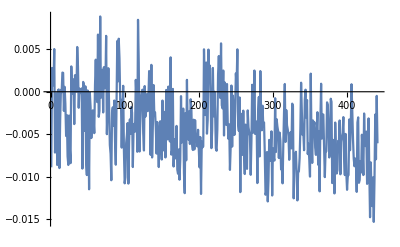

```mathematica
ListLinePlot[deltas[[1]]]
```

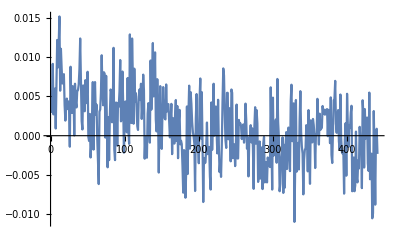

```mathematica
ListLinePlot[deltas[[400]]]
```

```mathematica
ListSeriesDelta[twosome_] := Table[twosome[[2,i]]-twosome[[1,i]], {i, 1, Length[twosome[[1]]]}]
```

```mathematica
test = {{1,2,3,4,5},{3,4,5,6,7}}
```

{{1,2,3,4,5},{3,4,5,6,7}}
 |  |  |  |

```mathematica
test[[1,1]]
```

1

```mathematica
ListSeriesDelta[test]
```

{2,2,2,2,2}

```mathematica
partitionedData2 := Partition[partitionedData, 2]
```

```mathematica
ListSeriesDelta[partitionedData2[[1]]]
```

{-0.00384521,0.0098877,0.0108032,0.00332642,0.011261,-0.000762939,-0.000610352,0.0106812,425,0.000793457,-0.00848389,-0.0103455,-0.00247192,-0.00384521,-0.00317383,0.00674438,-0.000335693}
 |  |  |  |

```mathematica
Length[partitionedData2[[1,1]]]
```

441

```mathematica
partitionedData3 := Partition[Map[ListSeriesDelta, partitionedData2], 2]
```

```mathematica
partitionedData4 := Partition[Map[ListSeriesDelta, partitionedData3], 2]
```

```mathematica
partitionedData5 := Partition[Map[ListSeriesDelta, partitionedData4], 2]
```

```mathematica
partitionedData6 := Partition[Map[ListSeriesDelta, partitionedData5], 2]
```

```mathematica
partitionedData7 := Partition[Map[ListSeriesDelta, partitionedData6], 2]
```

```mathematica
partitionedData8 := Partition[Map[ListSeriesDelta, partitionedData7], 2]
```

```mathematica
partitionedData9 := Partition[Map[ListSeriesDelta, partitionedData8], 2]
```

```mathematica
partitionedData10 := Partition[Map[ListSeriesDelta, partitionedData9], 2]
```

```mathematica
partitionedData11 := Partition[Map[ListSeriesDelta, partitionedData10], 2]
```

```mathematica
partitionedData12 := Partition[Map[ListSeriesDelta, partitionedData11], 2]
```

```mathematica
Length[Flatten[partitionedData10]]
```

882

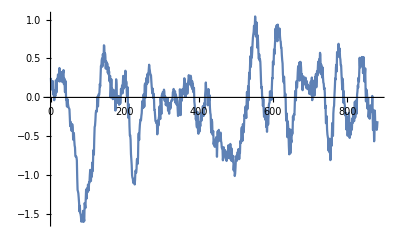

```mathematica
ListLinePlot[Flatten[partitionedData10]]
```

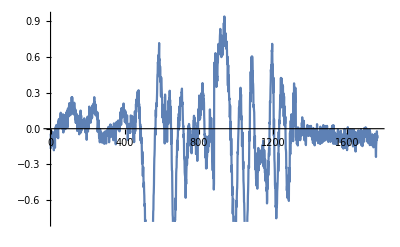

```mathematica
ListLinePlot[Flatten[partitionedData9]]
```

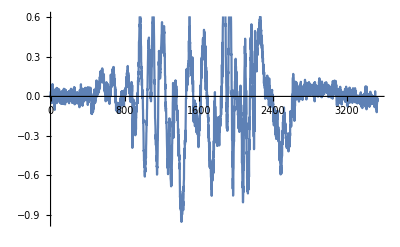

```mathematica
ListLinePlot[Flatten[partitionedData8]]
```

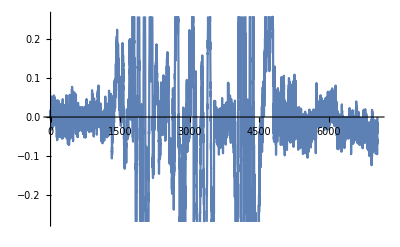

```mathematica
ListLinePlot[Flatten[partitionedData7]]
```

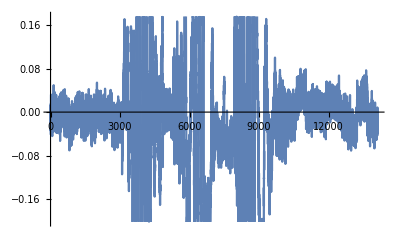

```mathematica
ListLinePlot[Flatten[partitionedData6]]
```

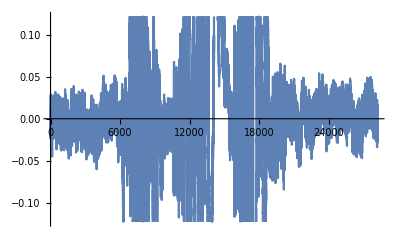

```mathematica
ListLinePlot[Flatten[partitionedData5]]
```

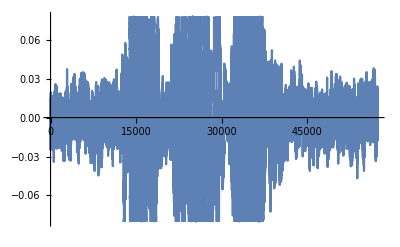

```mathematica
ListLinePlot[Flatten[partitionedData4]]
```

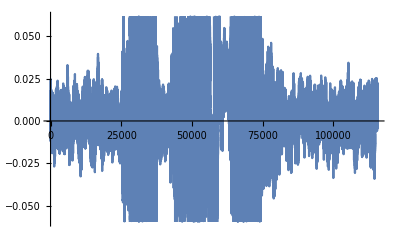

```mathematica
ListLinePlot[Flatten[partitionedData3]]
```

```mathematica
ListLinePlot[Flatten[partitionedData]]
```

-Graphics-

## Compose the delta function and the partition function to obtain a function that reduces the data

```mathematica
ReducePartitionedData =  Map[ListSeriesDelta, #]& @ Partition[#,2]&
```

(ListSeriesDelta/@#1&)[Partition[#1,2]]&
 |  |  |  |

```mathematica
resStandard = NestWhile[ReducePartitionedData , #, Length[#]>1&] & @ Partition[utt135[[1,1,1]], uttSampleWindowSize, windowStartInterval]
```

{{-0.794464,-0.760498,-0.67749,-0.711365,-0.770905,-0.720276,-0.608765,-0.834991,425,0.282867,-0.048645,-0.0264893,0.162933,0.105377,0.0159912,0.219391,0.261047}}
 |  |  |  |

```mathematica
res8 = NestWhile[ReducePartitionedData , #, Length[#]>1&] & @ Partition[utt135[[1,1,1]], 8, 2]
```

{{0.583221,-2.35056,-1.74783,1.46643,0.556976,-0.766968,0.643372,0.327911}}
 |  |  |  |

```mathematica
res50 = NestWhile[ReducePartitionedData , #, Length[#]>1&] & @ Partition[utt135[[1,1,1]], 50, 2]
```

{{0.583221,-2.35056,-1.74783,1.46643,0.556976,-0.766968,0.643372,0.327911,34,0.234589,0.217957,0.542175,0.198334,0.937714,0.432068,0.763092,-0.265381}}
 |  |  |  |

```mathematica
res250 = NestWhile[ReducePartitionedData , #, Length[#]>1&] & @ Partition[utt135[[1,1,1]], 250, 2]
```

{{0.583221,-2.35056,-1.74783,1.46643,0.556976,-0.766968,0.643372,0.327911,234,-0.327484,0.0410156,-1.35034,-1.5495,0.704315,0.749481,0.169678,2.33649}}
 |  |  |  |

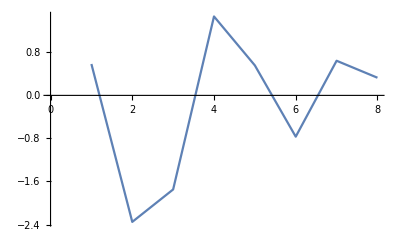
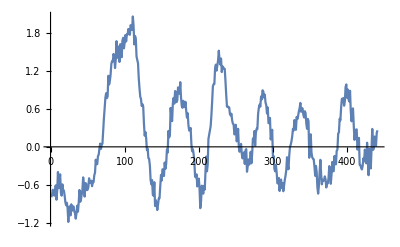
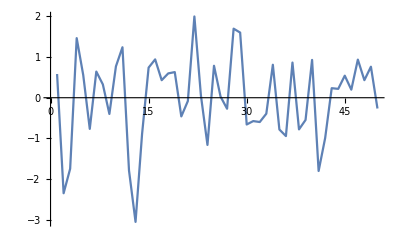
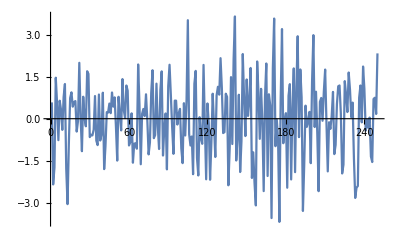

```mathematica
Map[ListLinePlot[#]&, {res8[[1]], resStandard, res50[[1]], res250[[1]]}]
```

```mathematica
res250020 = NestWhile[ReducePartitionedData , #, Length[#]>1&] & @ Partition[utt135[[1,1,1]], 250, 20]
```

{{-3.72131,-3.21304,-2.77704,-3.23755,-2.75089,-2.7135,-3.38574,-2.75873,234,0.709503,0.291077,0.785889,0.771484,0.399597,0.799896,1.04684,0.208038}}
 |  |  |  |

```mathematica
res250040 = NestWhile[ReducePartitionedData , #, Length[#]>1&] & @ Partition[utt135[[1,1,1]], 250, 40]
```

{{3.46735,2.86606,2.51257,2.52829,1.90601,1.72922,1.81238,1.47495,234,1.55817,1.89816,1.13342,0.803406,1.46494,0.970551,0.618042,1.45587}}
 |  |  |  |

```mathematica
res250060 = NestWhile[ReducePartitionedData , #, Length[#]>1&] & @ Partition[utt135[[1,1,1]], 250, 60]
```

{{2.49695,2.75525,2.12292,2.06848,2.56219,2.5141,2.30844,2.56985,234,1.38733,1.43829,1.37448,1.22205,1.3754,1.28381,1.53201,1.31326}}
 |  |  |  |

```mathematica
res250010 = NestWhile[ReducePartitionedData , #, Length[#]>1&] & @ Partition[utt135[[1,1,1]], 250, 10]
```

{{1.18793,0.954651,1.53387,0.719208,0.0709534,1.90866,2.11935,0.592621,234,-2.09143,-1.35547,-3.4093,-3.5076,-1.82779,-3.24225,-4.92456,-3.91388}}
 |  |  |  |

```mathematica
res25000 = NestWhile[ReducePartitionedData , #, Length[#]>1&] & @ Partition[utt135[[1,1,1]], 250, 1]
```

{{-2.93378,0.602722,3.21426,-0.909454,-1.32394,1.41034,-0.31546,-0.727295,234,0.3685,-1.39136,-0.199158,2.25381,0.045166,-0.579803,2.16681,0.449463}}
 |  |  |  |

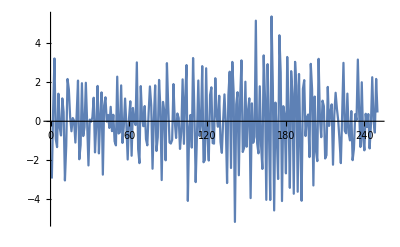
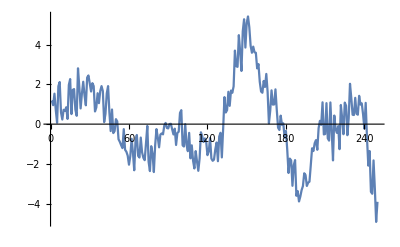
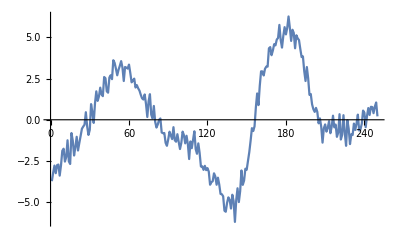
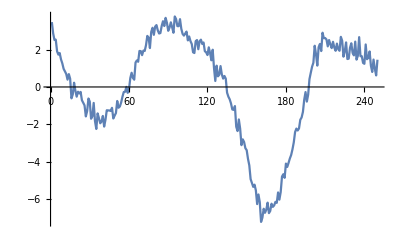
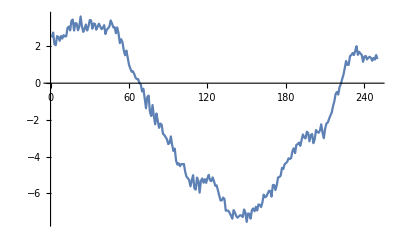
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[ListLinePlot[#]&, {res25000[[1]], res250[[1]], res250010[[1]], res250020[[1]], res250040[[1]], res250060[[1]]}]
```

## Determine deltas of deltas and any new deltas within resolution

use delta time resolution to filter deltas
deltass should be wrt middle